# Polarized Boson Gluon Fusion Computation

## FeynArts Amplitude Generation

```mathematica
$LoadAddOns={"FeynArts"};
<<FeynCalc`;
$CKM=True;
FAVerbose=0;
```

FeynCalc 10.2.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

loading generic model file /Users/edoardo/Library/Wolfram/Applications/FeynCalc/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/edoardo/Library/Wolfram/Applications/FeynCalc/FeynArts/Models/SMQCD.mod

loading classes model file /Users/edoardo/Library/Wolfram/Applications/FeynCalc/FeynArts/Models/SM.mod

$CKM=True

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counterterms of order 1

> 6 counterterms of order 2

classes model {SMQCD} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 2 Particles insertions

> Top. 1 aebf/cedf/ef.m, 0 diagrams

> Top. 2 aebf/cfde/ef.m, 0 diagrams

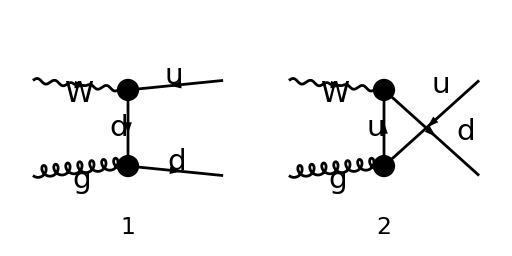

FeynArtsGraphics()(([1] | [2]))

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

(ⅈ e (φ(OverBar[k_2],m_2)).(γ̄)^μ.(v-a (γ̄)^5).(γ̄·(p̄-OverBar[k_1])+m_1).(-2 g_s (γ̄)^ν T_Col4Col3^Glu2).(φ(-OverBar[k_1],m_1)))/(2 ((OverBar[k_1]-p̄)^2-m_1^2))+(ⅈ e (φ(OverBar[k_2],m_2)).(-2 g_s (γ̄)^ν T_Col4Col3^Glu2).(γ̄·(OverBar[k_2]-p̄)+m_2).(γ̄)^μ.(v-a (γ̄)^5).(φ(-OverBar[k_1],m_1)))/(2 ((p̄-OverBar[k_2])^2-m_2^2))

{(ⅈ e (φ(OverBar[k_2],m_2)).(γ̄)^μ.(v-a (γ̄)^5).(γ̄·(p̄-OverBar[k_1])+m_1).(-2 g_s (γ̄)^ν T_Col4Col3^Glu2).(φ(-OverBar[k_1],m_1)))/(2 ((OverBar[k_1]-p̄)^2-m_1^2))+(ⅈ e (φ(OverBar[k_2],m_2)).(-2 g_s (γ̄)^ν T_Col4Col3^Glu2).(γ̄·(OverBar[k_2]-p̄)+m_2).(γ̄)^μ.(v-a (γ̄)^5).(φ(-OverBar[k_1],m_1)))/(2 ((p̄-OverBar[k_2])^2-m_2^2))}

```mathematica
SetMandelstam[s,t,u,q,p,-k2,-k1,I Q,0,SMP["m_d"],SMP["m_u"]];

(*Define box notation for k1 and k2*)
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";

(*Generate Feynman diagram topologies with specific vertex and fermion structures*)
LOW=InsertFields[CreateTopologies[0,2->2],{V[3],V[5]}->{-F[3,{1}],F[4,{1}]},InsertionLevel->{Particles},Model->"SMQCD"];

(*Paint the generated topologies with specific layout and settings*)
Paint[LOW,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}]

(*Convert Feynman amplitudes,applying options for dimension,polarization,and prefactors*)
convertedAmps=FCFAConvert[CreateFeynAmp[LOW],IncomingMomenta->{q,p},OutgoingMomenta->{k1,k2},ChangeDimension->4,List->False,SMP->True,TransversePolarizationVectors->{p},Contract->True,DropSumOver->True,Prefactor->Sqrt[2]*SMP["sin_W"]/(2 SMP["V_ud",-I])];

(*Replace specific DiracGamma structures to create the generic type of the interaction*)

substitution1={DiracGamma[Momentum[Polarization[p,I,Transversality->True]]].DiracGamma[7]->DiracGamma[Momentum[Polarization[p,I,Transversality->True]]],DiracGamma[Momentum[Polarization[p,I,Transversality->True]]].DiracGamma[6]->DiracGamma[Momentum[Polarization[p,I,Transversality->True]]],DiracGamma[7]->(v-a*GA[5])};

amp0=ReplaceAll[convertedAmps,substitution1];

(*Define the M_munu tensor cutting the polarization vectors*)

substitution2={DiracGamma[Momentum[Polarization[q,I]]]->GA[μ],DiracGamma[Momentum[Polarization[p,I,Transversality->True]]]->-I GA[ν]};
Mmunu=ReplaceAll[amp0,substitution2];

(*Substitute mass parameters for final tensor form*)
CuttedTensorGF=Mmunu/.{SMP["m_u"]->Subscript[m,1],SMP["m_d"]->Subscript[m,2]}
DumpSave["PolarizedCaseCuttedAmplitude.mx",{CuttedTensorGF}]

<<PolarizedCaseCuttedAmplitude.mx (*CuttedTensorGF*)
```

## Projectors

```mathematica
ClearScalarProducts[];

hatkmu=FV[p,μ]-(SP[p,q]/SP[q,q])FV[q,μ];
hatSmu=FV[S,μ]-SP[S,q]/SP[q,q] FV[q,μ];
hatknu=ReplaceAll[hatkmu,{μ->ν}];
hatSnu=ReplaceAll[hatSmu,{μ->ν}];


WF1pol=(-MT[μ,ν]+( FV[q,μ].FV[q,ν])/SP[q,q]) F1;
WF2pol=(hatkmu.hatknu)/(SP[p,q]) F2;
WF3pol=-I LC[μ,ν,α,β].FV[q,α].FV[p,β]/(2SP[p,q])F3;
WF4pol=-FV[q,μ].FV[q,ν]/SP[q] F4;
WF5pol=(FV[q,μ].FV[p,ν]+FV[p,μ].FV[q,ν])/(2 SP[p,q]) F5;


Wg1pol=I LC[μ,ν,α,β].FV[q,α].FV[S,β]/SP[p,q] g1;
Wg2pol= I LC[μ,ν,α,β].(FV[q,α]).(FV[S,β]- (SP[S,q]/SP[p,q]) FV[p,β])/SP[p,q] g2;
Wg3pol= (1/SP[P,q])((1/2) (hatkmu.hatSnu+hatSmu.hatknu)- (SP[S,q]/SP[p,q]) hatkmu.hatknu) g3;
Wg4pol= (SP[S,q]/SP[p,q] ) (hatkmu.hatknu/SP[p,q]) g4;
Wg5pol= (SP[S,q]/SP[p,q] ) (-MT[μ,ν]+FV[q,μ].FV[q,ν]/SP[q]) g5;
Wg6pol= (SP[S,q]/SP[p,q] ) (FV[q,μ].FV[q,ν]/SP[q]) g6;
Wg7pol= (SP[S,q]/SP[p,q] ) (FV[q,μ].FV[p,ν]+FV[p,μ].FV[q,ν])/(2 SP[p,q]) g7;


Wpol=WF1pol+WF2pol+WF3pol+WF4pol+WF5pol+Wg1pol+Wg4pol+Wg5pol+Wg6pol+Wg7pol;
averaged=((Wpol/.{S->-p})-(Wpol/.{S->p}))/2;
```

```mathematica
structuretest={g1,g4,g5,g6,g7};
coefficentest={a,b,c,d,e};
Projector= a MT[μ,ν]+b FV[q,μ].FV[q,ν]+c FV[p,μ].FV[p,ν]+d(FV[q,μ].FV[p,ν]+FV[p,μ].FV[q,ν])+e LC[μ,ν,α,β].FV[q,α].FV[p,β];
eqn=Projector.averaged//Contract;
solution[j_]:=Solve[Table[D[eqn,structuretest[[i]]]==KroneckerDelta[i,j],{i,1,Length[structuretest]}],coefficentest]

(*Useful substitutions to handle the LeviCivita contractions*)

LeviCivitasubDEN={1/Eps[LorentzIndex[μ], LorentzIndex[ν], Momentum[p], Momentum[q]]^2->1/Contract[Eps[LorentzIndex[μ],LorentzIndex[ν],Momentum[p],Momentum[q]].Eps[LorentzIndex[μ],LorentzIndex[ν],Momentum[p],Momentum[q]]]};

LeviCivitasubNUM={Eps[LorentzIndex[μ], LorentzIndex[ν], Momentum[p], Momentum[q]]^2->Contract[Eps[LorentzIndex[μ],LorentzIndex[ν],Momentum[p],Momentum[q]].Eps[LorentzIndex[μ],LorentzIndex[ν],Momentum[p],Momentum[q]]]};

(*Define the projectors*)

Pg1partonic=ReplaceAll[(Projector/.solution[1][[1]]),LeviCivitasubDEN]//Contract;
Pg4partonic=(Projector/.solution[2][[1]]); 
Pg5partonic=(Projector/.solution[3][[1]]);
Pg6partonic=(Projector/.solution[4][[1]]);
Pg7partonic=(Projector/.solution[5][[1]]);
```

```mathematica
(*Test*)
```

```mathematica
ReplaceAll[Pg1partonic.averaged//Contract,LeviCivitasubNUM]//FullSimplify
Pg4partonic.averaged//Contract//FullSimplify
Pg5partonic.averaged//Contract//FullSimplify
Pg6partonic.averaged//Contract//FullSimplify
Pg7partonic.averaged//Contract//FullSimplify
```

g1

g4

g5

g6

g7

## Semi Inclusive Structure Functions Computation

```mathematica
ClearScalarProducts[];
SetMandelstam[s,t,u,q,p,-k2,-k1,I Q,0,Subscript[m, 2],Subscript[m, 1]];
$Assumptions={Subscript[m, 1]>0,Subscript[m, 2]>0};
```

```mathematica
PolarizedProjector= I LC[μ,ν,α,β].FV[p,α].FV[q,β]/( 2 SP[p,q])//Contract; (*Definition in the Felix Heckorn PhD Thesis*)

EvaluateContraction[projector1_,projector2_,Tensor_]:=Module[{expression,simplified},(*General approach to constructing the expression*)expression=(projector1/.{ν->k1}).(projector2/.{μ->ν,ν->k2}).(Tensor).(ComplexConjugate[ReplaceAll[Tensor,{μ->k1,ν->k2,v->v1,a->a1}]])//Contract;
(*Simplify the expression*)simplified=SUNSimplify[expression//FeynAmpDenominatorExplicit,Explicit->True,SUNNToCACF->True]//FermionSpinSum//DiracSimplify/.{SUNN->3};
(*Return the simplified expression*)simplified]
```

```mathematica
prefactor=(1/8)(2 Pi/SMP["g_s"]^2); (*Average of the incoming color and Paper Convention*)
```

```mathematica
(*g1semicomputed= prefactor EvaluateContraction[Pg1partonic,PolarizedProjector,CuttedTensorGF];
g4semicomputed=prefactor EvaluateContraction[Pg4partonic,PolarizedProjector,CuttedTensorGF];
g5semicomputed=prefactor EvaluateContraction[Pg5partonic,PolarizedProjector,CuttedTensorGF];
g6semicomputed=prefactor EvaluateContraction[Pg6partonic,PolarizedProjector,CuttedTensorGF];
g7semicomputed=prefactor EvaluateContraction[Pg7partonic,PolarizedProjector,CuttedTensorGF];
DumpSave["WilsonCoefficientsBGFPolarized.mx",{g1semicomputed,g4semicomputed,g5semicomputed,g6semicomputed,g7semicomputed}];*)

<<WilsonCoefficientsBGFPolarized.mx
```

Get::noopen: Cannot open WilsonCoefficientsBGFPolarized.mx.

$Failed

## Semi Inclusive Structure Functions as written in the paper

## Useful Definitions & Functions in order to simplify the expressions

```mathematica
topaper={t-> Subscript[m, 1]^2-Q^2/OverHat[x](1-ζ),u->Subscript[m, 2]^2- ζ Q^2/OverHat[x],s-> Q^2( 1/OverHat[x]-1)};

toζ[Hg_]:=SUNSimplify[ReplaceAll[Hg,topaper]//FullSimplify,SUNNToCACF->False]/.{SUNN->3,SMP["e"]->1};


qplus=a a1+v v1;
Rplus=(a1 v+ a v1)/2;

Σpp=Q^2+Subscript[m, 2]^2+Subscript[m, 1]^2;
Σpm=Q^2+Subscript[m, 2]^2-Subscript[m, 1]^2;
Σmp=Q^2-Subscript[m, 2]^2+Subscript[m, 1]^2;

kallen[a_,b_,c_]:=Sqrt[a^2+b^2+c^2-2 a b-2 a c-2 b c];
Δ=kallen[Subscript[m, 1]^2,Subscript[m, 2]^2,-Q^2];


(*Functions usefuls for obtaining the expressions as reported in the paper*)


toζsplitted[Hg_]:=ApartImproved[SUNSimplify[ReplaceAll[Hg,topaper]//FullSimplify,SUNNToCACF->False]/.{SUNN->3,SMP["e"]->1}]

ToPolynomial[list_,var_]:=
        var^Range[0,Length[list]-1].list

ApartImproved[test1_]:=Module[{variables,Base,toBase,mat,list,new,ext},variables={Y0,Y1,Y0s,Y1s};
Base={1/ζ,1/(ζ-1),1/ζ^2,1/(ζ-1)^2};
toBase={1/ζ->Y0,1/(ζ-1)->Y1,1/ζ^2->Y0s,1/(ζ-1)^2->Y1s};
ext=Table[D[Apart[test1,ζ]/.toBase,variables[[i]]],{i,1,4}];
mat=CoefficientList[ext,x̂]//FullSimplify;
list=ToPolynomial[#,x̂]&/@mat;
new=Inner[Times,Base,list,Plus]+FullSimplify[Limit[test1,{ζ->Infinity}]];
new]
```

## Paper Coefficients Check

```mathematica
Clear[s,ξ];
```

```mathematica
exchange={Subscript[m, 1]->Subscript[m, 2],Subscript[m, 2]->Subscript[m, 1]};
basis={1/(1-ζ)^2,1/ζ^2,1/(1-ζ),1/ζ,1};
```

```mathematica
PolarizedSplittingFunctionqg[x_]:= (2x-1)/2;
λ=Q^2/( Subscript[m, 2]^2+Q^2);
```

```mathematica
Ag1paper= OverHat[x] Subscript[m, 1]^2/Q^2;
Bg1paper=Ag1paper/.exchange;
Cg1paper=(PolarizedSplittingFunctionqg[OverHat[x]/λ]- Ag1paper);
Dg1paper=Cg1paper/.exchange;
Eg1paper= - 2 PolarizedSplittingFunctionqg[OverHat[x]];


Ag5paper=-2 Ag1paper;
Bg5paper=-Ag5paper/.exchange;
Cg5paper=-2 Cg1paper;
Dg5paper=-Cg5paper/.exchange;
Eg5paper=0;

Ag6paper=(Subscript[m, 2]^2-Subscript[m, 1]^2)/Q^2 Ag5paper;
Bg6paper=-Ag6paper/.exchange;
Cg6paper=(Subscript[m, 2]^2-Subscript[m, 1]^2)/Q^2 (Cg5paper+2 Ag5paper);
Dg6paper=-Cg6paper/.exchange;
Eg6paper=0;

Ag4paper=2OverHat[x]( Ag5paper+Ag6paper);
Bg4paper=-Ag4paper/.exchange;
Cg4paper=2OverHat[x](Cg5paper+Cg6paper);
Dg4paper=-Cg4paper/.exchange;
Eg4paper=0;

Ag7paper= -2 Ag6paper;
Bg7paper=-Ag7paper/.exchange;
Cg7paper=- 2 Cg6paper;
Dg7paper=-Cg7paper/.exchange;
Eg7paper=0;
```

```mathematica
coefficientsg1paper={Ag1paper,Bg1paper,Cg1paper,Dg1paper,Eg1paper};
coefficientsg4paper={Ag4paper,Bg4paper,Cg4paper,Dg4paper,Eg4paper};
coefficientsg5paper={Ag5paper,Bg5paper,Cg5paper,Dg5paper,Eg5paper};
coefficientsg6paper={Ag6paper,Bg6paper,Cg6paper,Dg6paper,Eg6paper};
coefficientsg7paper={Ag7paper,Bg7paper,Cg7paper,Dg7paper,Eg7paper};
```

```mathematica
k={qplus,Rplus,Rplus,Rplus,Rplus}; (*Subscript[k, i] coefficients reported in the paper*)
```

```mathematica
g1semipaper=( 4 Pi k[[1]])basis.coefficientsg1paper;
g4semipaper=( 4 Pi k[[2]]) basis.coefficientsg4paper;
g5semipaper=( 4 Pi k[[3]]) basis.coefficientsg5paper;
g6semipaper=( 4 Pi k[[4]])basis.coefficientsg6paper;
g7semipaper=( 4 Pi k[[5]]) basis.coefficientsg7paper;
```

```mathematica
Solve[toζ[g1semicomputed]-y g1semipaper==0,y]//FullSimplify
Solve[toζ[g4semicomputed]-y g4semipaper==0,y]//FullSimplify
Solve[toζ[g5semicomputed]-y g5semipaper==0,y]//FullSimplify
Solve[toζ[g6semicomputed]-y g6semipaper==0,y]//FullSimplify
Solve[toζ[g7semicomputed]-y g7semipaper==0,y]//FullSimplify
```

{{y→-((ζ-1)^2 ζ^2 g1semicomputed Q^2)/(2 π (2 (ζ-1) ζ+1) (a a1+v v1) (-2 ζ m_1^2 x̂+2 (ζ-1) m_2^2 x̂+(ζ-1) ζ Q^2 (2 x̂-1)))}}

{{y→((ζ-1)^2 ζ^2 g4semicomputed Q^4)/(4 π x̂ (-m_1^2+m_2^2+(2 ζ-1) Q^2) (a v1+a1 v) (-2 ζ m_1^2 x̂+2 (ζ-1) m_2^2 x̂+(ζ-1) ζ Q^2 (2 x̂-1)))}}

{{y→((ζ-1)^2 ζ^2 g5semicomputed Q^2)/(2 π (2 ζ-1) (a v1+a1 v) (-2 ζ m_1^2 x̂+2 (ζ-1) m_2^2 x̂+(ζ-1) ζ Q^2 (2 x̂-1)))}}

{{y→((ζ-1)^2 ζ^2 g6semicomputed Q^4)/(2 π (m_1^2-m_2^2) (a v1+a1 v) (2 x̂ (ζ m_1^2-(ζ-1) (m_2^2+ζ Q^2))+(ζ-1) ζ Q^2))}}

{{y→-((ζ-1)^2 ζ^2 g7semicomputed Q^4)/(4 π (m_1^2-m_2^2) (a v1+a1 v) (2 x̂ (ζ m_1^2-(ζ-1) (m_2^2+ζ Q^2))+(ζ-1) ζ Q^2))}}

## ACOT scheme: subtraction terms

```mathematica
Clear[s]
```

```mathematica
$Assumptions={s>0};
ζ1=1+(Subscript[m, 2]^2-Subscript[m, 1]^2)/s;
ζ2=kallen[Subscript[m, 1]^2,Subscript[m, 2]^2,s]/s;
ζplus= 1/2( ζ1+ζ2);
ζminus=1/2( ζ1-ζ2);
```

```mathematica
baseinclusive={(ζplus-ζminus)/((1-ζplus)(1-ζminus)),(ζplus-ζminus)/(ζplus ζminus), Log[(1-ζminus)/(1-ζplus)], Log[ζplus/ζminus], (ζplus-ζminus)};
additionalprefactor=(1/2);
```

```mathematica
phasespace=additionalprefactor 1/(8 Pi) ;
```

```mathematica
g1inclusive= baseinclusive.coefficientsg1paper;
g4inclusive= baseinclusive.coefficientsg4paper;
g5inclusive=baseinclusive.coefficientsg5paper;
g6inclusive= baseinclusive.coefficientsg6paper;
g7inclusive= baseinclusive.coefficientsg7paper;
```

## Limits for m_1→ 0

```mathematica
c1paper=1;
c4paper=2 OverHat[x](c5paper+c6paper);
c5paper=-1;
c6paper= -Subscript[m, 2]^2/(Q^2);
c7paper=- 2 c6paper;
lambda1=λ/.{Subscript[m, 2]->Subscript[m, 1]};
ξ=x/OverHat[x];

Normal[Series[2 Cg1paper,{Subscript[m, 1],0,0}]]-c1paper PolarizedSplittingFunctionqg[OverHat[x]/λ]//Simplify
Normal[Series[Cg4paper,{Subscript[m, 1],0,0}]]-  c4paper  PolarizedSplittingFunctionqg[OverHat[x]/λ]//Simplify
Normal[Series[Cg5paper,{Subscript[m, 1],0,0}]]-  c5paper  PolarizedSplittingFunctionqg[OverHat[x]/λ]//Simplify
Normal[Series[Cg6paper,{Subscript[m, 1],0,0}]]- c6paper  PolarizedSplittingFunctionqg[OverHat[x]/λ]//Simplify
Normal[Series[Cg7paper,{Subscript[m, 1],0,0}]]-  c7paper  PolarizedSplittingFunctionqg[OverHat[x]/λ]//Simplify

Normal[Series[2Cg1paper,{Subscript[m, 2],0,0}]]-  (c1paper  PolarizedSplittingFunctionqg[OverHat[x]/λ])/.{Subscript[m, 1]->Subscript[m, 2]}//Simplify
Normal[Series[Cg4paper,{Subscript[m, 2],0,0}]]-  (c4paper  PolarizedSplittingFunctionqg[OverHat[x]/λ])/.{Subscript[m, 1]->Subscript[m, 2]}//Simplify
Normal[Series[Cg5paper,{Subscript[m, 2],0,0}]]- (c5paper  PolarizedSplittingFunctionqg[OverHat[x]/λ])/.{Subscript[m, 1]->Subscript[m, 2]}//Simplify
Normal[Series[Cg6paper,{Subscript[m, 2],0,0}]]- (c6paper  PolarizedSplittingFunctionqg[OverHat[x]/λ])/.{Subscript[m, 1]->Subscript[m, 2]}//Simplify
Normal[Series[Cg7paper,{Subscript[m, 2],0,0}]]- (c7paper  PolarizedSplittingFunctionqg[OverHat[x]/λ])/.{Subscript[m, 1]->Subscript[m, 2]}//Simplify





(*Series[Normal[Series[Cg1paper-Dg1paper,{Subscript[m, 1],0,0}]],{Subscript[m, 2],0,0}]
Series[Normal[Series[Cg4paper+Dg4paper,{Subscript[m, 1],0,0}]],{Subscript[m, 2],0,0}]
Series[Normal[Series[Cg5paper+Dg5paper,{Subscript[m, 1],0,0}]],{Subscript[m, 2],0,0}]
Series[Normal[Series[Cg6paper+Dg6paper,{Subscript[m, 1],0,0}]],{Subscript[m, 2],0,0}]
Series[Normal[Series[Cg7paper+Dg7paper,{Subscript[m, 1],0,0}]],{Subscript[m, 2],0,0}]*)
```

(m_2^2 x̂)/Q^2+x̂-1/2

-(x̂ (m_2^2+Q^2) (2 x̂ (m_2^2+Q^2)-Q^2))/Q^4

1/2-(x̂ (m_2^2+Q^2))/Q^2

-(m_2^2 (2 x̂ (m_2^2+Q^2)-Q^2))/(2 Q^4)

(m_2^2 (2 x̂ (m_2^2+Q^2)-Q^2))/Q^4

-(3 m_2^2 x̂)/Q^2+x̂-1/2

(x̂ (-3 m_2^2 Q^2-2 x̂ (-6 m_2^2 Q^2-3 m_2^4+Q^4)+Q^4))/Q^4

x̂ ((3 m_2^2)/Q^2-1)+1/2

(3 m_2^2 (2 x̂ (m_2^2+Q^2)-Q^2))/(2 Q^4)

-(3 m_2^2 (2 x̂ (m_2^2+Q^2)-Q^2))/Q^4

## Literature Check (Felix Heckorn Thesis)

## Loading Literature Expressions

```mathematica
ClearScalarProducts[];

SetMandelstam[s,t,u,q,p,-k2,-k1,I Q,0,m,m];
sp=s-SP[q];
u1=u-m^2;
up=u1-SP[q];
t1=t-m^2;


(*Calculations are performed for neutral currents*)
```

```mathematica
BVVF2=(-1-(6 SP[q])/sp-(6 SP[q]^2)/(sp^2)+(SP[q] (6 m^2+s)+2 m^2 s+(sp^2)/2)/(t1 u1)-((2 m^2+SP[q]) m^2 sp^2)/(t1 u1)^2)+(ε/2)(-1+(s^2-SP[q] sp)/(t1 u1)-(m^2 SP[q] sp^2)/(t1^2 u1^2))+ε^2 (sp^2)/(8 t1 u1);

BVVFL=-(4 SP[q])/sp ((s/sp)-(m^2 sp)/(t1 u1));

BVVg1=(1+(2 SP[q])/sp -(sp (2 (2 m^2+SP[q])+sp)/(2 t1 u1))+(m^2 sp^3)/(t1 u1)^2)+ε ((-1/2+sp/(4 t1 u1))) (1+ε);

BAAF2=(m^2 sp^(1/2) (1+ε) (2+ε) (12 m^2 (-1+ε)+SP[q] (-6+(-3+ε) ε)))/(12 (t1 u1)^2)+((1+ε)/(4 SP[q] sp^2) (8 s sp^(3 ε)+12 SP[q]^3 (2+ε)+12 SP[q]^2 sp (2+ε)+SP[q] sp^(2) (4 ε (20-(-3+ε) ε))))-((1+ε)/(48 SP[q] (t1 u1)) (SP[q] (2+ε) (-6+(-3+ε) ε) (4 SP[q]^2+4 SP[q] sp+sp (2+ε))+48 m^2 (-s^(2-ε)+SP[q]^(2) (-4+ε) (2+ε)+SP[q] sp (-2+ε+ε^2))));

BAAFL=-((m^2 sp^2 (1+ε) (2+ε) (12 m^2+SP[q] ε))/(6 (t1 u1)^2))-((1+ε) (4 sp^3+4 SP[q]^3 (2+ε)+4 SP[q]^2 sp (2+ε)+SP[q] sp^(2) ε(6+ε)))/(2 SP[q] sp^2)+((1+ε)/(24 SP[q] (t1 u1)) (24 m^2 (sp^2 (-2+ε)+4 SP[q]^2 (2+ε)+2 SP[q] sp (2+ε))+SP[q] ε (2+ε) (4 SP[q]^2+4 SP[q] sp+sp^2 (2+ε))));

BAAg1=((1+ε) (2-ε))/2 B[V,V,g1];

BVAF3=-((1+ε) (2+ε) (t1^2-u1^2))*(-m^2 SP[q]/(2 (t1 u1)^2)+(4 SP[q] (SP[q]+sp)+sp^2 (2+ε))/(8 sp^(2) t1 u1));

BVAg4=(1+ε) (t1-u1)*(-m^2 sp^2/(t1 u1)^2+(4 SP[q]+sp (2-ε))/(4 t1 u1));

BVAgL=0;
```

```mathematica
PF2literature=-MT[μ,ν]/(n-2)-(n-1)/(n-2) (4z^2/SP[q] FV[p,μ].FV[p,ν])- FV[q,μ].FV[q,ν]/SP[q]- (n-2)/(n-1) ((2z/SP[q])(FV[q,μ].FV[p,ν]+FV[q,ν].FV[p,μ]));
PFLliterature=- (4z^2 FV[p,μ].FV[p,ν])/SP[q]-FV[q,μ].FV[q,ν]/SP[q]-(2z(FV[q,μ].FV[p,ν]+FV[q,ν].FV[p,μ]))/SP[q];
PF3zliterature=- I z LC[μ,ν,α,β].FV[p,α].FV[q,β]/SP[q];

Pg1zliterature=PF3zliterature//Contract;
Pg4literature=-PF2literature;
PgLliterature=-PFLliterature;
```

```mathematica
PF2g=PFLg=PF3zg=- MT[μ,ν];
Pg1zg=Pg4g=PgLg=2 I LC[μ,ν,α,β].FV[p,α].FV[q,β]/( 2 SP[p,q])//Contract;
```

## Check

```mathematica
(*Cross check is performed considering ε=0*)
```

### Felix Projectors check

```mathematica
z=Q^2/(2 SP[q, p]);
```

```mathematica
(2z)( Pg4literature.averaged)/.{n->4}//Contract//Simplify  
(Pg4partonic.averaged)//Contract//Simplify
(*It's important to notice that 2g6+g7=0: so the Felix Projectors are ok*)
```

g4-(5 Q^2 (2 g6+g7))/(3 (Q^2+s))

g4

```mathematica
ReplaceAll[(Pg1zliterature.averaged)/.{n->4}//Contract,LeviCivitasubNUM]//Simplify (* g1 projector in the paper is not right*)
ReplaceAll[(Pg1partonic.averaged)//Contract,LeviCivitasubNUM]//Simplify
```

-g1

g1

### Semi Inclusive Structure Functions check

```mathematica
(*In this code the born terms are computed as prescribed in the paper
FelixTensorGF=  CuttedTensorGF/.{Subscript[m, 1]->m,Subscript[m, 2]->m};
(*Felix Tensor but using our prefactor convention*)

(*BornTermF2=EvaluateContraction[(PF2literature/.{n->4}),PF2g,FelixTensorGF];
BornTermFL=EvaluateContraction[(PFLliterature/.{n->4}),PFLg,FelixTensorGF];
BornTermF3z=EvaluateContraction[(PF3zliterature/.{n->4}),PF3zg,FelixTensorGF];
BornTermgL=EvaluateContraction[(PgLliterature/.{n->4}),PgLg,FelixTensorGF];
BornTermg1z=EvaluateContraction[(Pg1zliterature/.{n->4}),Pg1zg,FelixTensorGF];
BornTermg4=EvaluateContraction[(Pg4literature/.{n->4}),Pg4g,FelixTensorGF];

DumpSave["WilsonCoefficientsBGFPolarizedLiterature.mx",{BornTermF2,BornTermFL,BornTermF3z,BornTermg4,BornTermgL,BornTermg1z}];*)

(*Numerical Check*)
(*N[ReplaceAll[ BornTermFL,numerical]/.{a->0}]
N[ReplaceAll[8  BVVFL,numerical]] (*ok*)

N[ReplaceAll[ BornTermF2,numerical]/.{a->0}]
N[ReplaceAll[  8 BVVF2,numerical]] (*ok*)

N[ReplaceAll[ BornTermF3z,numerical]]
N[ReplaceAll[ 8 BVAF3,numerical]](*Factor 2, and minus sign is missing*)

N[ReplaceAll[ BornTermg1z,numerical]]
N[ReplaceAll[ 8 BVVg1,numerical]] (* Minus sign is not consistent*)

N[ReplaceAll[  BornTermg4,numerical]]
N[ReplaceAll[   8 BVAg4,numerical]](*Factor 2 missing*)
s=2m^2 -Q^2 -(u+t);
  numerical={u->3,t->1,Q->2,m->5,n->4,ε->0};
*)*)

<<WilsonCoefficientsBGFPolarizedLiterature.mx
```

Get::noopen: Cannot open WilsonCoefficientsBGFPolarizedLiterature.mx.

$Failed

```mathematica
toζequalmasses={t-> m^2-Q^2/OverHat[x](1-ζ),u->  m^2-ζ Q^2/OverHat[x],s-> Q^2( 1/OverHat[x]-1),ε->0};

Solve[Simplify[(g1semipaper/.{Subscript[m, 1]->m,Subscript[m, 2]->m})]-b Simplify[( 8  BVVg1/.toζequalmasses)]==0,b]//FullSimplify
Solve[ (g4semipaper/.{Subscript[m, 1]->m,Subscript[m, 2]->m})-b( 8 (2OverHat[x])  BVAg4/.toζequalmasses)==0,b]//Simplify

(*Proportionalilty factor between Felix Thesis and our paper*)
```

{{b→1/2 π (a a1+v v1)}}

{{b→1/2 π (a v1+a1 v)}}

## Numerical Test

```mathematica
Clear[s]
```

```mathematica
s=Q^2(1/OverHat[x]-1);

m1sub=1.3;
m2sub=4.5;

Δ/.{Subscript[m, 1]->m1sub,Subscript[m, 2]->m2sub,Q->1}
```

19.732

```mathematica
(coefficientsg1paper.baseinclusive)/.{Subscript[m, 1]->m1sub,Subscript[m, 2]->m2sub,Q->1,OverHat[x]->0.2}
 (coefficientsg4paper.baseinclusive)/.{Subscript[m, 1]->m1sub,Subscript[m, 2]->m2sub,Q->1,OverHat[x]->0.2}
 (coefficientsg5paper.baseinclusive)/.{Subscript[m, 1]->m1sub,Subscript[m, 2]->m2sub,Q->1,OverHat[x]->0.2}
 (coefficientsg6paper.baseinclusive)/.{Subscript[m, 1]->m1sub,Subscript[m, 2]->m2sub,Q->1,OverHat[x]->0.2}
 (coefficientsg7paper.baseinclusive)/.{Subscript[m, 1]->m1sub,Subscript[m, 2]->m2sub,Q->1,OverHat[x]->0.2}
```

-9.64482

44.3571

11.86

99.0328

-198.066

```mathematica
additionalprefactor= (1/2);
```

```mathematica
g1GFinclusive=additionalprefactor coefficientsg1paper.baseinclusive;
g4GFinclusive=additionalprefactor coefficientsg4paper.baseinclusive;
g5GFinclusive=additionalprefactor coefficientsg5paper.baseinclusive;
g6GFinclusive=additionalprefactor coefficientsg6paper.baseinclusive;
g7GFinclusive=additionalprefactor coefficientsg7paper.baseinclusive;
```

```mathematica
Save["/Users/edoardo/Desktop/GitHub/Heavy-Quark-Production-in-ACOT-scheme/Polarized/PolarizedGluonFusion.m",{g1GFinclusive,g4GFinclusive,g5GFinclusive,g6GFinclusive,g7GFinclusive}];
```

```mathematica
$Assumptions={Subscript[m, 2]>0,Subscript[m, 1]>0,Q>0, 0<OverHat[x]<1};
```

```mathematica
Series[Series[Log[ζplus/ζminus],{Subscript[m, 1],0,0}],{Subscript[m, 2],0,0}]
Series[Series[Simplify[Log[(1-ζminus)/(1-ζplus)]],{Subscript[m, 2],0,0}],{Subscript[m, 1],0,0}]
```

((-2 log(m_2)+2 log(Q)+log(1-x̂)-log(x̂))+O(m_2^1))+O(m_1^1)

((-2 log(m_1)+2 log(Q)+log(1-x̂)-log(x̂))+O(m_1^1))+O(m_2^1)